```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

g::shdw: Symbol g appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

IncludeObj::shdw: Symbol IncludeObj appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

MultipleIsoperimetricEdges::shdw: Symbol MultipleIsoperimetricEdges appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

NumBasis::shdw: Symbol NumBasis appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

GroundingScheme::shdw: Symbol GroundingScheme appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

GroundingRandom::shdw: Symbol GroundingRandom appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

GroundingPreviousMax::shdw: Symbol GroundingPreviousMax appears in multiple contexts {GraphPartition`,Global`}; definitions in context GraphPartition` may shadow or be shadowed by other definitions.

Global`

```mathematica
Graphics3D[{Arrow[{{0,0,0},d}],Arrow[{{0,0,0},v}],Arrow[{{0,0,0},len*dd}],Line[{len*dd,v}]},Axes->True]
```

-Graphics3D-

```mathematica
sym=LineGraph[GridGraph[{5,5}]];
```

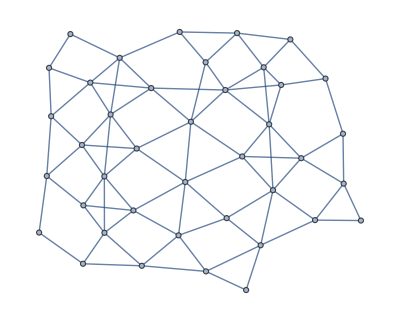

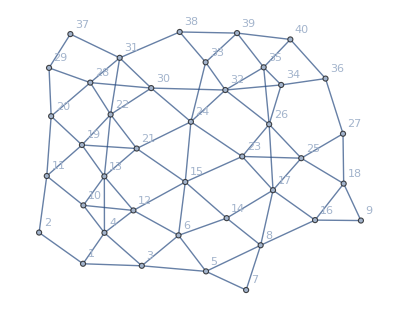

```mathematica
g = EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]]
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
```

```mathematica
basisVectors = FingerprintVectors[g,3]
```

{{0.301029,-0.504451,0.370264},{0.175933,-1.07388,1.32327},{0.376382,-0.255818,0.00127054},{0.326526,-0.144452,-0.226113},{0.433375,-0.200155,-0.0485922},{0.420354,-0.135017,-0.102836},{0.512072,-0.187169,-0.0337605},{0.479143,-0.17043,-0.056571},{0.520757,-0.164709,-0.0233099},{0.24166,0.0516696,0.426175},{0.0687023,1.51688,0.883962},{0.371233,-0.0526715,-0.288784},{0.318079,0.0782117,-1.65185},{0.453981,-0.109708,-0.103092},{0.442552,-0.0175344,-0.0873431},{0.492898,-0.145488,-0.0531987},{0.493464,-0.0979061,-0.0421816},{0.533055,-0.122272,0.0046695},{0.312248,0.542406,-0.0937561},{0.302689,0.700574,0.279993},{0.430295,0.167517,-0.0290986},{0.417229,0.288043,0.0358545},{0.48498,-0.0188804,-0.0245875},{0.470222,0.0827523,0.0119794},{0.51775,-0.0783491,-0.000207889},{0.516595,-0.0289306,0.0235339},{0.536412,-0.0845576,0.0251664},{0.409869,0.357302,0.133626},{0.395692,0.424903,0.183781},{0.460634,0.175508,0.0642425},{0.448855,0.23668,0.0918989},{0.502635,0.038672,0.0427446},{0.490747,0.0887978,0.0569917},{0.529121,-0.037046,0.039287},{0.524244,-0.00985023,0.0480732},{0.541475,-0.0613643,0.044557},{0.450272,0.256032,0.125363},{0.482024,0.145713,0.0880491},{0.513977,0.0405429,0.0655829},{0.534647,-0.0232903,0.0568577}}

```mathematica
iv = VectorPartition[basisVectors,V[g]/2, OptimizationOn->False,
				OptimizationObj-> (CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,iv,0.5]]
dir=Normalize[Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

{0.854363,0.475786,0.209027}

```mathematica
(**)
ds=Table[
With[{iv=VectorMaxOnDirection[basisVectors,V[g]/2,{Cos[2*Pi/40*i],Sin[2*Pi/200*i]}, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]},
Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
,{i,200}];
```

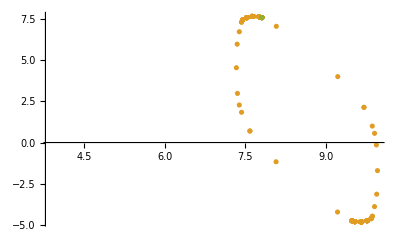

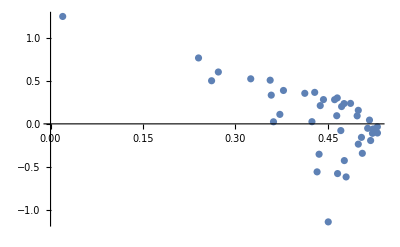

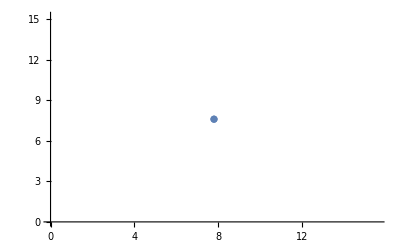

```mathematica
ListPlot[{basisVectors,ds,{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}}]
ListPlot[basisVectors]
ListPlot[{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}]
```

#### Idea - Mallow+Random Projection - KMeans + Linear combination of mean vectors?

```mathematica
(**)
newiv=VectorMaxOnDirection[basisVectors,V[g]/2,dir, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

{11,20,29,28,37,31,19,22,38,30,33,39,40,32,35,24,36,34,21,26,27,25,23,18,17,9,15,7,16,10,8,14,6,5,12,3,4,1,13,2}

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

```mathematica
newiv=VectorPartition[basisVectors,V[g]/2, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&),
Method->MallowProbe]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1}

40.

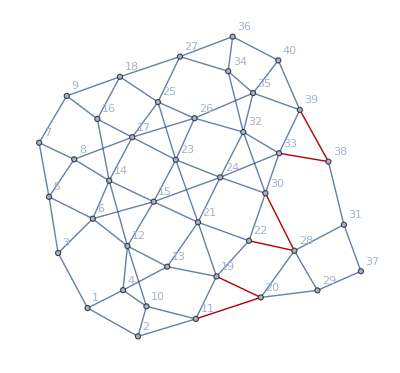

```mathematica
ShowSpectralCut[g]
```

```mathematica
N[SpectralEdges[g,IncludeObj->True]]
```

{41.0256,{6.<->14.,6.<->15.,7.<->8.,12.<->14.,12.<->15.,13.<->21.,19.<->21.,19.<->22.,20.<->29.}}

```mathematica
{grounds, basis}= IsoperimetricBasis[g,3,GroundingPreviousMax]
```

{{15,40,2},{{0.154238,0.12125,-0.269505},{0.168177,0.0904752,-0.639202},{0.137119,0.152234,-0.05576},{0.139987,0.146178,-0.0784168},{0.136629,0.140012,0.0365467},{0.10019,0.226634,0.123473},{0.148611,0.107064,0.0383402},{0.143161,0.099254,0.0752712},{0.179843,-0.0233795,0.0396271},{0.142649,0.137684,-0.0767159},{0.164683,0.0848385,-0.238344},{0.108125,0.213499,0.0679814},{0.140369,0.13136,-0.0229468},{0.101644,0.201783,0.174084},{0.,0.450779,0.429651},{0.165697,0.016944,0.0594459},{0.145793,0.0556044,0.103077},{0.176557,-0.0385652,0.0549459},{0.155282,0.0919039,-0.0734485},{0.175191,0.0444281,-0.128871},{0.119837,0.160801,0.0812618},{0.158899,0.06323,-0.0232055},{0.122875,0.102317,0.162298},{0.127202,0.0918713,0.131396},{0.161409,-0.0128576,0.0890759},{0.16254,-0.0486761,0.0934248},{0.181845,-0.10983,0.0667721},{0.17648,0.0184401,-0.0635328},{0.186885,0.00766761,-0.105021},{0.165209,0.0139974,0.00945745},{0.178784,-0.0119848,-0.0348863},{0.167247,-0.0664319,0.0726531},{0.170613,-0.0850961,0.0681946},{0.179568,-0.147745,0.078191},{0.180915,-0.197805,0.0903918},{0.190138,-0.252929,0.091432},{0.191551,-0.0147275,-0.0875226},{0.18435,-0.115726,0.0255093},{0.18622,-0.22496,0.0783572},{0.191569,-0.476075,0.16447}}}

```mathematica
Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingRandom]][[1]],100]]

Mean[Table[N[MultipleIsoperimetricEdges[g,NumBasis->3, IncludeObj->True,GroundingScheme->GroundingPreviousMax]][[1]],100]]
```

44.4316

41.9713

```mathematica
Range[3]
```

{1,2,3}